# Call Python to compute CY metrics

Getting started
The easiest thing to get started would be to just run the entire notebook.

Documentation
• To see all functions currently available run ?cymetric
• If you want to see detailed documentation for any of the functions (including its input, options, output, examples), run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values. 
• The value of all global options can be checked with GetGlobalOptions[]

Setting up the program
In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and (older versions of) Mathematica, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, with an extension “.m”, at the same location as the notebook file) that stores some options, e.g. the location of the virtual environment to use for future runs.
More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package from the web.
You can also download the package file and copy it to Mathematica’s Application folder. 
To find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and load it with  <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Desktop*)
PathToVenv=FileNameJoin[{$HomeDirectory,"Desktop/mathematica-venv"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

Mathematica discovered the following Python environments on your system:

Looking for Python 3

Found Python version 3.9.10 at /Library/Frameworks/Python.framework/Versions/Current/bin/python3.9.

Creating virtual environment at /Users/ruehle/Desktop/mathematica-venv

Upgrading pip, wheel, setuptools...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,VolJNorm→1}

Now we generate some points. We set the output Directory to “Quintic”

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
ChangeSetting["Dir","Quintic"];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
res=GeneratePoints[poly,{4},"Points"->100000,"KahlerModuli"->{1},"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False). 
We also set Verbose to 3 to see some more info during the training process.

```mathematica
history=TrainNN["Epochs"->50,"EvaluateModel"->True,"Verbose"->3];
```

DEBUG:mathematica:{'ActivationFunctions': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'Alphas': array([1., 1., 1., 1., 1.]), 'BatchSize': 64, 'Dir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'DisableGPU': False, 'HiddenLayers': array([64, 64, 64]), 'LearningRate': 0.001, 'Model': 'PhiFS', 'Precision': 10, 'PrintLosses': array([ True,  True,  True,  True,  True]), 'PrintMeasures': array([ True,  True,  True,  True,  True]), 'Python': '/Users/ruehle/venv-mathematica/bin/python', 'Verbose': 3, 'Epochs': 50, 'EvaluateModel': True, 'logger_level': 10}

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential_3"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica: Layer (type)                Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica: dense_12 (Dense)            (None, 64)                704

DEBUG:mathematica:

DEBUG:mathematica: dense_13 (Dense)            (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_14 (Dense)            (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_15 (Dense)            (None, 1)                 65

DEBUG:mathematica:

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,089

DEBUG:mathematica:Trainable params: 9,089

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

- Sigma measure val:      0.2079

- Kaehler measure val:    6.1054e-15

- Transition measure val: 0.0488

- Ricci measure val:      1.0613

- Volk val:               5.2866

Epoch 1/50

- Sigma measure val:      0.1459

- Kaehler measure val:    5.7592e-15

- Transition measure val: 0.0123

- Ricci measure val:      1.7360

- Volk val:               5.0933

1407/1407 - 21s - sigma_loss: 0.1654 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0133 - ricci_loss: 0.0000e+00 - sigma_val: 0.1459 - kaehler_val: 5.7592e-15 - transition_val: 0.0123 - ricci_val: 1.7360 - volk_val: 5.0933 - 21s/epoch - 15ms/step

Epoch 2/50

- Sigma measure val:      0.1425

- Kaehler measure val:    5.7666e-15

- Transition measure val: 0.0119

- Ricci measure val:      1.5290

- Volk val:               4.7816

1407/1407 - 17s - sigma_loss: 0.1471 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0122 - ricci_loss: 0.0000e+00 - sigma_val: 0.1425 - kaehler_val: 5.7666e-15 - transition_val: 0.0119 - ricci_val: 1.5290 - volk_val: 4.7816 - 17s/epoch - 12ms/step

Epoch 3/50

- Sigma measure val:      0.1147

- Kaehler measure val:    6.3662e-15

- Transition measure val: 0.0073

- Ricci measure val:      1.2160

- Volk val:               4.8569

1407/1407 - 17s - sigma_loss: 0.1197 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0084 - ricci_loss: 0.0000e+00 - sigma_val: 0.1147 - kaehler_val: 6.3662e-15 - transition_val: 0.0073 - ricci_val: 1.2160 - volk_val: 4.8569 - 17s/epoch - 12ms/step

Epoch 4/50

- Sigma measure val:      0.1062

- Kaehler measure val:    6.4606e-15

- Transition measure val: 0.0063

- Ricci measure val:      1.0924

- Volk val:               4.9309

1407/1407 - 17s - sigma_loss: 0.1033 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0066 - ricci_loss: 0.0000e+00 - sigma_val: 0.1062 - kaehler_val: 6.4606e-15 - transition_val: 0.0063 - ricci_val: 1.0924 - volk_val: 4.9309 - 17s/epoch - 12ms/step

Epoch 5/50

- Sigma measure val:      0.0981

- Kaehler measure val:    6.3911e-15

- Transition measure val: 0.0070

- Ricci measure val:      0.8691

- Volk val:               4.9658

1407/1407 - 17s - sigma_loss: 0.0965 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0062 - ricci_loss: 0.0000e+00 - sigma_val: 0.0981 - kaehler_val: 6.3911e-15 - transition_val: 0.0070 - ricci_val: 0.8691 - volk_val: 4.9658 - 17s/epoch - 12ms/step

Epoch 6/50

- Sigma measure val:      0.0910

- Kaehler measure val:    6.4514e-15

- Transition measure val: 0.0056

- Ricci measure val:      0.6624

- Volk val:               4.9692

1407/1407 - 18s - sigma_loss: 0.0879 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0066 - ricci_loss: 0.0000e+00 - sigma_val: 0.0910 - kaehler_val: 6.4514e-15 - transition_val: 0.0056 - ricci_val: 0.6624 - volk_val: 4.9692 - 18s/epoch - 13ms/step

Epoch 7/50

- Sigma measure val:      0.0867

- Kaehler measure val:    6.3488e-15

- Transition measure val: 0.0052

- Ricci measure val:      0.6157

- Volk val:               4.9098

1407/1407 - 18s - sigma_loss: 0.0817 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0061 - ricci_loss: 0.0000e+00 - sigma_val: 0.0867 - kaehler_val: 6.3488e-15 - transition_val: 0.0052 - ricci_val: 0.6157 - volk_val: 4.9098 - 18s/epoch - 13ms/step

Epoch 8/50

- Sigma measure val:      0.0867

- Kaehler measure val:    6.3724e-15

- Transition measure val: 0.0048

- Ricci measure val:      0.6108

- Volk val:               4.8648

1407/1407 - 18s - sigma_loss: 0.0775 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0051 - ricci_loss: 0.0000e+00 - sigma_val: 0.0867 - kaehler_val: 6.3724e-15 - transition_val: 0.0048 - ricci_val: 0.6108 - volk_val: 4.8648 - 18s/epoch - 13ms/step

Epoch 9/50

- Sigma measure val:      0.0846

- Kaehler measure val:    6.1847e-15

- Transition measure val: 0.0038

- Ricci measure val:      0.6070

- Volk val:               4.8747

1407/1407 - 17s - sigma_loss: 0.0745 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0042 - ricci_loss: 0.0000e+00 - sigma_val: 0.0846 - kaehler_val: 6.1847e-15 - transition_val: 0.0038 - ricci_val: 0.6070 - volk_val: 4.8747 - 17s/epoch - 12ms/step

Epoch 10/50

- Sigma measure val:      0.0821

- Kaehler measure val:    6.0281e-15

- Transition measure val: 0.0036

- Ricci measure val:      0.6076

- Volk val:               4.8326

1407/1407 - 19s - sigma_loss: 0.0723 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0036 - ricci_loss: 0.0000e+00 - sigma_val: 0.0821 - kaehler_val: 6.0281e-15 - transition_val: 0.0036 - ricci_val: 0.6076 - volk_val: 4.8326 - 19s/epoch - 13ms/step

Epoch 11/50

- Sigma measure val:      0.0794

- Kaehler measure val:    6.1095e-15

- Transition measure val: 0.0031

- Ricci measure val:      0.6103

- Volk val:               4.9098

1407/1407 - 18s - sigma_loss: 0.0706 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0033 - ricci_loss: 0.0000e+00 - sigma_val: 0.0794 - kaehler_val: 6.1095e-15 - transition_val: 0.0031 - ricci_val: 0.6103 - volk_val: 4.9098 - 18s/epoch - 13ms/step

Epoch 12/50

- Sigma measure val:      0.0789

- Kaehler measure val:    6.0818e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.6143

- Volk val:               4.8140

1407/1407 - 18s - sigma_loss: 0.0692 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0031 - ricci_loss: 0.0000e+00 - sigma_val: 0.0789 - kaehler_val: 6.0818e-15 - transition_val: 0.0030 - ricci_val: 0.6143 - volk_val: 4.8140 - 18s/epoch - 13ms/step

Epoch 13/50

- Sigma measure val:      0.0782

- Kaehler measure val:    6.0541e-15

- Transition measure val: 0.0032

- Ricci measure val:      0.6185

- Volk val:               4.8527

1407/1407 - 17s - sigma_loss: 0.0675 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0782 - kaehler_val: 6.0541e-15 - transition_val: 0.0032 - ricci_val: 0.6185 - volk_val: 4.8527 - 17s/epoch - 12ms/step

Epoch 14/50

- Sigma measure val:      0.0779

- Kaehler measure val:    6.0334e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.6070

- Volk val:               4.8654

1407/1407 - 17s - sigma_loss: 0.0662 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0779 - kaehler_val: 6.0334e-15 - transition_val: 0.0030 - ricci_val: 0.6070 - volk_val: 4.8654 - 17s/epoch - 12ms/step

Epoch 15/50

- Sigma measure val:      0.0745

- Kaehler measure val:    6.0944e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.5826

- Volk val:               4.8903

1407/1407 - 17s - sigma_loss: 0.0649 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0745 - kaehler_val: 6.0944e-15 - transition_val: 0.0028 - ricci_val: 0.5826 - volk_val: 4.8903 - 17s/epoch - 12ms/step

Epoch 16/50

- Sigma measure val:      0.0738

- Kaehler measure val:    6.0927e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.5550

- Volk val:               4.9002

1407/1407 - 18s - sigma_loss: 0.0636 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0738 - kaehler_val: 6.0927e-15 - transition_val: 0.0026 - ricci_val: 0.5550 - volk_val: 4.9002 - 18s/epoch - 13ms/step

Epoch 17/50

- Sigma measure val:      0.0709

- Kaehler measure val:    6.0221e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.5327

- Volk val:               4.8515

1407/1407 - 18s - sigma_loss: 0.0621 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0709 - kaehler_val: 6.0221e-15 - transition_val: 0.0028 - ricci_val: 0.5327 - volk_val: 4.8515 - 18s/epoch - 13ms/step

Epoch 18/50

- Sigma measure val:      0.0691

- Kaehler measure val:    6.1408e-15

- Transition measure val: 0.0031

- Ricci measure val:      0.5275

- Volk val:               4.8813

1407/1407 - 18s - sigma_loss: 0.0610 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0691 - kaehler_val: 6.1408e-15 - transition_val: 0.0031 - ricci_val: 0.5275 - volk_val: 4.8813 - 18s/epoch - 13ms/step

Epoch 19/50

- Sigma measure val:      0.0681

- Kaehler measure val:    6.0948e-15

- Transition measure val: 0.0029

- Ricci measure val:      0.5296

- Volk val:               4.8927

1407/1407 - 17s - sigma_loss: 0.0598 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0031 - ricci_loss: 0.0000e+00 - sigma_val: 0.0681 - kaehler_val: 6.0948e-15 - transition_val: 0.0029 - ricci_val: 0.5296 - volk_val: 4.8927 - 17s/epoch - 12ms/step

Epoch 20/50

- Sigma measure val:      0.0674

- Kaehler measure val:    6.1164e-15

- Transition measure val: 0.0029

- Ricci measure val:      0.5010

- Volk val:               4.8780

1407/1407 - 18s - sigma_loss: 0.0588 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0031 - ricci_loss: 0.0000e+00 - sigma_val: 0.0674 - kaehler_val: 6.1164e-15 - transition_val: 0.0029 - ricci_val: 0.5010 - volk_val: 4.8780 - 18s/epoch - 13ms/step

Epoch 21/50

- Sigma measure val:      0.0657

- Kaehler measure val:    6.2069e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.5240

- Volk val:               4.9681

1407/1407 - 18s - sigma_loss: 0.0577 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0031 - ricci_loss: 0.0000e+00 - sigma_val: 0.0657 - kaehler_val: 6.2069e-15 - transition_val: 0.0028 - ricci_val: 0.5240 - volk_val: 4.9681 - 18s/epoch - 13ms/step

Epoch 22/50

- Sigma measure val:      0.0655

- Kaehler measure val:    6.1485e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.4849

- Volk val:               4.8451

1407/1407 - 18s - sigma_loss: 0.0564 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0655 - kaehler_val: 6.1485e-15 - transition_val: 0.0030 - ricci_val: 0.4849 - volk_val: 4.8451 - 18s/epoch - 13ms/step

Epoch 23/50

- Sigma measure val:      0.0624

- Kaehler measure val:    6.2087e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.5097

- Volk val:               4.9042

1407/1407 - 18s - sigma_loss: 0.0553 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0624 - kaehler_val: 6.2087e-15 - transition_val: 0.0028 - ricci_val: 0.5097 - volk_val: 4.9042 - 18s/epoch - 13ms/step

Epoch 24/50

- Sigma measure val:      0.0601

- Kaehler measure val:    6.2425e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.5026

- Volk val:               4.9292

1407/1407 - 17s - sigma_loss: 0.0539 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0030 - ricci_loss: 0.0000e+00 - sigma_val: 0.0601 - kaehler_val: 6.2425e-15 - transition_val: 0.0030 - ricci_val: 0.5026 - volk_val: 4.9292 - 17s/epoch - 12ms/step

Epoch 25/50

- Sigma measure val:      0.0593

- Kaehler measure val:    6.3590e-15

- Transition measure val: 0.0029

- Ricci measure val:      0.5063

- Volk val:               4.9590

1407/1407 - 18s - sigma_loss: 0.0526 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0029 - ricci_loss: 0.0000e+00 - sigma_val: 0.0593 - kaehler_val: 6.3590e-15 - transition_val: 0.0029 - ricci_val: 0.5063 - volk_val: 4.9590 - 18s/epoch - 13ms/step

Epoch 26/50

- Sigma measure val:      0.0562

- Kaehler measure val:    6.3893e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.4808

- Volk val:               4.9472

1407/1407 - 18s - sigma_loss: 0.0510 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0029 - ricci_loss: 0.0000e+00 - sigma_val: 0.0562 - kaehler_val: 6.3893e-15 - transition_val: 0.0026 - ricci_val: 0.4808 - volk_val: 4.9472 - 18s/epoch - 13ms/step

Epoch 27/50

- Sigma measure val:      0.0551

- Kaehler measure val:    6.3795e-15

- Transition measure val: 0.0025

- Ricci measure val:      0.4923

- Volk val:               4.9513

1407/1407 - 18s - sigma_loss: 0.0495 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0028 - ricci_loss: 0.0000e+00 - sigma_val: 0.0551 - kaehler_val: 6.3795e-15 - transition_val: 0.0025 - ricci_val: 0.4923 - volk_val: 4.9513 - 18s/epoch - 13ms/step

Epoch 28/50

- Sigma measure val:      0.0533

- Kaehler measure val:    6.3826e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.4681

- Volk val:               4.9772

1407/1407 - 18s - sigma_loss: 0.0483 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0028 - ricci_loss: 0.0000e+00 - sigma_val: 0.0533 - kaehler_val: 6.3826e-15 - transition_val: 0.0030 - ricci_val: 0.4681 - volk_val: 4.9772 - 18s/epoch - 13ms/step

Epoch 29/50

- Sigma measure val:      0.0533

- Kaehler measure val:    6.4687e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4804

- Volk val:               4.9337

1407/1407 - 18s - sigma_loss: 0.0469 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0028 - ricci_loss: 0.0000e+00 - sigma_val: 0.0533 - kaehler_val: 6.4687e-15 - transition_val: 0.0024 - ricci_val: 0.4804 - volk_val: 4.9337 - 18s/epoch - 13ms/step

Epoch 30/50

- Sigma measure val:      0.0502

- Kaehler measure val:    6.4089e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4860

- Volk val:               4.9392

1407/1407 - 19s - sigma_loss: 0.0457 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0028 - ricci_loss: 0.0000e+00 - sigma_val: 0.0502 - kaehler_val: 6.4089e-15 - transition_val: 0.0028 - ricci_val: 0.4860 - volk_val: 4.9392 - 19s/epoch - 13ms/step

Epoch 31/50

- Sigma measure val:      0.0485

- Kaehler measure val:    6.4296e-15

- Transition measure val: 0.0032

- Ricci measure val:      0.4658

- Volk val:               4.9605

1407/1407 - 18s - sigma_loss: 0.0445 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - ricci_loss: 0.0000e+00 - sigma_val: 0.0485 - kaehler_val: 6.4296e-15 - transition_val: 0.0032 - ricci_val: 0.4658 - volk_val: 4.9605 - 18s/epoch - 13ms/step

Epoch 32/50

- Sigma measure val:      0.0486

- Kaehler measure val:    6.4900e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4683

- Volk val:               4.9261

1407/1407 - 17s - sigma_loss: 0.0435 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - ricci_loss: 0.0000e+00 - sigma_val: 0.0486 - kaehler_val: 6.4900e-15 - transition_val: 0.0028 - ricci_val: 0.4683 - volk_val: 4.9261 - 17s/epoch - 12ms/step

Epoch 33/50

- Sigma measure val:      0.0483

- Kaehler measure val:    6.4929e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4797

- Volk val:               4.9567

1407/1407 - 20s - sigma_loss: 0.0424 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - ricci_loss: 0.0000e+00 - sigma_val: 0.0483 - kaehler_val: 6.4929e-15 - transition_val: 0.0024 - ricci_val: 0.4797 - volk_val: 4.9567 - 20s/epoch - 14ms/step

Epoch 34/50

- Sigma measure val:      0.0477

- Kaehler measure val:    6.4309e-15

- Transition measure val: 0.0030

- Ricci measure val:      0.4375

- Volk val:               4.9069

1407/1407 - 19s - sigma_loss: 0.0418 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - ricci_loss: 0.0000e+00 - sigma_val: 0.0477 - kaehler_val: 6.4309e-15 - transition_val: 0.0030 - ricci_val: 0.4375 - volk_val: 4.9069 - 19s/epoch - 14ms/step

Epoch 35/50

- Sigma measure val:      0.0459

- Kaehler measure val:    6.5000e-15

- Transition measure val: 0.0023

- Ricci measure val:      0.4412

- Volk val:               4.9338

1407/1407 - 19s - sigma_loss: 0.0408 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - ricci_loss: 0.0000e+00 - sigma_val: 0.0459 - kaehler_val: 6.5000e-15 - transition_val: 0.0023 - ricci_val: 0.4412 - volk_val: 4.9338 - 19s/epoch - 13ms/step

Epoch 36/50

- Sigma measure val:      0.0431

- Kaehler measure val:    6.5155e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4262

- Volk val:               4.9496

1407/1407 - 19s - sigma_loss: 0.0401 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - ricci_loss: 0.0000e+00 - sigma_val: 0.0431 - kaehler_val: 6.5155e-15 - transition_val: 0.0027 - ricci_val: 0.4262 - volk_val: 4.9496 - 19s/epoch - 13ms/step

Epoch 37/50

- Sigma measure val:      0.0429

- Kaehler measure val:    6.4493e-15

- Transition measure val: 0.0023

- Ricci measure val:      0.4238

- Volk val:               4.9743

1407/1407 - 20s - sigma_loss: 0.0390 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0025 - ricci_loss: 0.0000e+00 - sigma_val: 0.0429 - kaehler_val: 6.4493e-15 - transition_val: 0.0023 - ricci_val: 0.4238 - volk_val: 4.9743 - 20s/epoch - 14ms/step

Epoch 38/50

- Sigma measure val:      0.0436

- Kaehler measure val:    6.5245e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4092

- Volk val:               4.9248

1407/1407 - 19s - sigma_loss: 0.0383 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0025 - ricci_loss: 0.0000e+00 - sigma_val: 0.0436 - kaehler_val: 6.5245e-15 - transition_val: 0.0024 - ricci_val: 0.4092 - volk_val: 4.9248 - 19s/epoch - 13ms/step

Epoch 39/50

- Sigma measure val:      0.0410

- Kaehler measure val:    6.5962e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.4142

- Volk val:               4.9804

1407/1407 - 18s - sigma_loss: 0.0375 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0025 - ricci_loss: 0.0000e+00 - sigma_val: 0.0410 - kaehler_val: 6.5962e-15 - transition_val: 0.0026 - ricci_val: 0.4142 - volk_val: 4.9804 - 18s/epoch - 13ms/step

Epoch 40/50

- Sigma measure val:      0.0399

- Kaehler measure val:    6.6799e-15

- Transition measure val: 0.0022

- Ricci measure val:      0.4103

- Volk val:               4.9738

1407/1407 - 19s - sigma_loss: 0.0367 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - ricci_loss: 0.0000e+00 - sigma_val: 0.0399 - kaehler_val: 6.6799e-15 - transition_val: 0.0022 - ricci_val: 0.4103 - volk_val: 4.9738 - 19s/epoch - 13ms/step

Epoch 41/50

- Sigma measure val:      0.0394

- Kaehler measure val:    6.4888e-15

- Transition measure val: 0.0019

- Ricci measure val:      0.3963

- Volk val:               4.9885

1407/1407 - 20s - sigma_loss: 0.0359 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - ricci_loss: 0.0000e+00 - sigma_val: 0.0394 - kaehler_val: 6.4888e-15 - transition_val: 0.0019 - ricci_val: 0.3963 - volk_val: 4.9885 - 20s/epoch - 14ms/step

Epoch 42/50

- Sigma measure val:      0.0373

- Kaehler measure val:    6.6323e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.3905

- Volk val:               4.9939

1407/1407 - 18s - sigma_loss: 0.0350 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - ricci_loss: 0.0000e+00 - sigma_val: 0.0373 - kaehler_val: 6.6323e-15 - transition_val: 0.0028 - ricci_val: 0.3905 - volk_val: 4.9939 - 18s/epoch - 13ms/step

Epoch 43/50

- Sigma measure val:      0.0375

- Kaehler measure val:    6.5910e-15

- Transition measure val: 0.0023

- Ricci measure val:      0.3911

- Volk val:               5.0046

1407/1407 - 18s - sigma_loss: 0.0342 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - ricci_loss: 0.0000e+00 - sigma_val: 0.0375 - kaehler_val: 6.5910e-15 - transition_val: 0.0023 - ricci_val: 0.3911 - volk_val: 5.0046 - 18s/epoch - 13ms/step

Epoch 44/50

- Sigma measure val:      0.0363

- Kaehler measure val:    6.4997e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.3802

- Volk val:               4.9685

1407/1407 - 19s - sigma_loss: 0.0336 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0023 - ricci_loss: 0.0000e+00 - sigma_val: 0.0363 - kaehler_val: 6.4997e-15 - transition_val: 0.0024 - ricci_val: 0.3802 - volk_val: 4.9685 - 19s/epoch - 13ms/step

Epoch 45/50

- Sigma measure val:      0.0357

- Kaehler measure val:    6.5324e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.3764

- Volk val:               4.9540

1407/1407 - 19s - sigma_loss: 0.0327 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0023 - ricci_loss: 0.0000e+00 - sigma_val: 0.0357 - kaehler_val: 6.5324e-15 - transition_val: 0.0026 - ricci_val: 0.3764 - volk_val: 4.9540 - 19s/epoch - 14ms/step

Epoch 46/50

- Sigma measure val:      0.0344

- Kaehler measure val:    6.5990e-15

- Transition measure val: 0.0025

- Ricci measure val:      0.3781

- Volk val:               5.0155

1407/1407 - 19s - sigma_loss: 0.0320 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0023 - ricci_loss: 0.0000e+00 - sigma_val: 0.0344 - kaehler_val: 6.5990e-15 - transition_val: 0.0025 - ricci_val: 0.3781 - volk_val: 5.0155 - 19s/epoch - 13ms/step

Epoch 47/50

- Sigma measure val:      0.0333

- Kaehler measure val:    6.4218e-15

- Transition measure val: 0.0021

- Ricci measure val:      0.3676

- Volk val:               4.9516

1407/1407 - 19s - sigma_loss: 0.0313 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - ricci_loss: 0.0000e+00 - sigma_val: 0.0333 - kaehler_val: 6.4218e-15 - transition_val: 0.0021 - ricci_val: 0.3676 - volk_val: 4.9516 - 19s/epoch - 13ms/step

Epoch 48/50

- Sigma measure val:      0.0328

- Kaehler measure val:    6.4065e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.3651

- Volk val:               4.9812

1407/1407 - 18s - sigma_loss: 0.0305 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - ricci_loss: 0.0000e+00 - sigma_val: 0.0328 - kaehler_val: 6.4065e-15 - transition_val: 0.0026 - ricci_val: 0.3651 - volk_val: 4.9812 - 18s/epoch - 13ms/step

Epoch 49/50

- Sigma measure val:      0.0319

- Kaehler measure val:    6.4249e-15

- Transition measure val: 0.0017

- Ricci measure val:      0.3658

- Volk val:               4.9905

1407/1407 - 19s - sigma_loss: 0.0299 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - ricci_loss: 0.0000e+00 - sigma_val: 0.0319 - kaehler_val: 6.4249e-15 - transition_val: 0.0017 - ricci_val: 0.3658 - volk_val: 4.9905 - 19s/epoch - 14ms/step

Epoch 50/50

- Sigma measure val:      0.0306

- Kaehler measure val:    6.2995e-15

- Transition measure val: 0.0021

- Ricci measure val:      0.3562

- Volk val:               4.9433

1407/1407 - 21s - sigma_loss: 0.0294 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0021 - ricci_loss: 0.0000e+00 - sigma_val: 0.0306 - kaehler_val: 6.2995e-15 - transition_val: 0.0021 - ricci_val: 0.3562 - volk_val: 4.9433 - 21s/epoch - 15ms/step

Writing training information to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
pts=GetPoints["all"];
pts[[1]]
```

{0.505163-0.356915 ⅈ,1.,-0.381408+0.844062 ⅈ,-0.0301477-0.0714962 ⅈ,-0.694855+0.131758 ⅈ}

We can access the weights of the points with respect to the auxiliary measure and the trained CY metric. 
The distribution should become peaked for the CY metric around a single value, since J^3 and Ω^2 are proportional.

```mathematica
weights=GetWeights["all"];
weightsCY=GetCYWeights["all"];
```

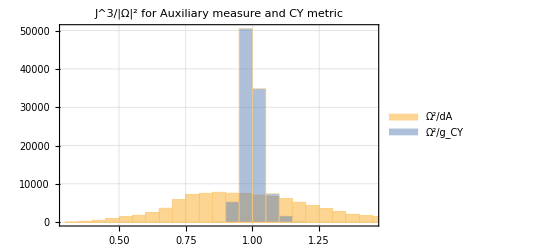

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for Auxiliary measure and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
metrics=CYMetric[{{1,2,3,4,5}}];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
metrics=CYMetric[pts];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.101506-3.31056×10^-9 ⅈ | 0.0155227+0.0106905 ⅈ | 0.0037985-0.00554964 ⅈ
0.0155227-0.0106905 ⅈ | 0.187597-3.84171×10^-9 ⅈ | -0.0423601+0.00179139 ⅈ
0.0037985+0.00554964 ⅈ | -0.0423601-0.00179139 ⅈ | 0.110954+1.32422×10^-9 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
gFSs[[1,2]]
```

{-0.705793+0.332496 ⅈ,-0.928077+0.0363186 ⅈ,0.167752-0.171312 ⅈ,0.11988-0.335881 ⅈ,1.}

```mathematica
auxWeights=GetAuxiliaryWeights["all"];
gFSs=FSMetric[pts,{1}];
gCYs=CYMetric[pts];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      4.9

For the Phi Model, we can also get the Kahler potential

```mathematica
kahler=GetKahlerPotential[pts];
kahler[[;;10]]
```

{-16.0002,-16.0101,-16.0486,-16.036,-16.0302,-15.998,-15.9596,-15.9724,-15.9852,-15.9797}

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.165381,0.147129,0.119693,0.103313,0.0964776,0.0879369,0.0817234,0.0774625,0.0745278,0.0723021,0.0706111,0.0692036,0.0674704,0.0661937,0.0649358,0.0635545,0.0620761,0.0610008,0.0598424,0.0588,0.0576927,0.0564197,0.055285,0.0538816,0.0525901,0.0509816,0.0495225,0.0482939,0.0469149,0.0457346,0.0444707,0.0434523,0.0424443,0.0417526,0.0408466,0.0400949,0.0390289,0.0382647,0.0375432,0.0366914,0.0359414,0.0350128,0.0342396,0.0335784,0.0326801,0.0320294,0.0312935,0.0305056,0.0299281,0.0294028},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.0133259,0.012225,0.00835527,0.00656947,0.00615438,0.00658627,0.00608556,0.00506319,0.00421501,0.00364111,0.00328311,0.00309857,0.00302269,0.00299992,0.0030206,0.00301953,0.00302683,0.00303732,0.00306322,0.00308054,0.00307337,0.00304797,0.00300394,0.00296007,0.0028949,0.00287692,0.00282711,0.00281224,0.002775,0.0027521,0.00271882,0.0026958,0.00265693,0.00264456,0.00260711,0.00257185,0.00254353,0.00251238,0.00248681,0.00244844,0.00241365,0.00239791,0.00235439,0.0023282,0.00229751,0.00227173,0.00222872,0.00220912,0.00215049,0.00214763},ricci_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},sigma_val→{0.145946,0.1425,0.114655,0.106215,0.098092,0.0909825,0.0866833,0.0867338,0.0846372,0.0820643,0.0793968,0.0789389,0.0781649,0.0779406,0.0745056,0.0738385,0.0708922,0.0691274,0.068127,0.0674302,0.0656614,0.065455,0.0624088,0.060095,0.0593405,0.056242,0.0550744,0.0532639,0.0532924,0.0501589,0.0485078,0.0485605,0.0482659,0.0476674,0.0459087,0.0430607,0.0428692,0.0436418,0.0410426,0.0399403,0.0394299,0.0373051,0.0374909,0.0362899,0.0357039,0.0344013,0.0332713,0.0327642,0.0319297,0.0306212},kaehler_val→{5.75916×10^-15,5.76663×10^-15,6.36616×10^-15,6.46065×10^-15,6.39113×10^-15,6.45139×10^-15,6.34879×10^-15,6.37242×10^-15,6.18468×10^-15,6.02814×10^-15,6.10947×10^-15,6.08179×10^-15,6.05413×10^-15,6.03343×10^-15,6.09442×10^-15,6.09269×10^-15,6.02212×10^-15,6.14084×10^-15,6.09483×10^-15,6.11638×10^-15,6.20693×10^-15,6.14848×10^-15,6.20868×10^-15,6.24255×10^-15,6.35898×10^-15,6.38932×10^-15,6.37951×10^-15,6.38263×10^-15,6.46868×10^-15,6.40894×10^-15,6.42956×10^-15,6.48999×10^-15,6.49294×10^-15,6.43089×10^-15,6.5×10^-15,6.51548×10^-15,6.44933×10^-15,6.52451×10^-15,6.59622×10^-15,6.67995×10^-15,6.48877×10^-15,6.63228×10^-15,6.59101×10^-15,6.49968×10^-15,6.53241×10^-15,6.59897×10^-15,6.42177×10^-15,6.40655×10^-15,6.42491×10^-15,6.29949×10^-15},transition_val→{0.012279,0.0119184,0.0072708,0.00625603,0.00695792,0.00561831,0.00518565,0.00475251,0.00376456,0.00357014,0.00311779,0.00299256,0.00321281,0.00300776,0.00277564,0.00255445,0.0028309,0.00310558,0.0028746,0.00288097,0.00276441,0.00298491,0.0027954,0.00302486,0.00294169,0.0026139,0.00254728,0.00303019,0.00240303,0.00278425,0.00321162,0.002764,0.00238258,0.00300285,0.00232257,0.00266143,0.00228254,0.00244194,0.00263614,0.00223073,0.00193288,0.00282143,0.00231457,0.00235315,0.00259678,0.00250739,0.0021297,0.00256697,0.00168029,0.00208701},ricci_val→{1.73602,1.52899,1.21599,1.09242,0.869059,0.662387,0.615687,0.610793,0.60702,0.607644,0.610278,0.614331,0.618527,0.607032,0.582566,0.555018,0.532738,0.527524,0.529585,0.500975,0.524011,0.484929,0.509717,0.502552,0.506264,0.480752,0.49234,0.468136,0.480417,0.485979,0.465775,0.468349,0.479747,0.437521,0.441163,0.426232,0.42381,0.40922,0.414213,0.410318,0.396302,0.39054,0.391111,0.380205,0.376425,0.378052,0.367622,0.36509,0.365825,0.356245},volk_val→{5.09328,4.78164,4.85694,4.93089,4.96575,4.96915,4.90984,4.86483,4.87474,4.8326,4.90977,4.81402,4.85266,4.86538,4.89026,4.90017,4.85147,4.88135,4.89273,4.87802,4.96813,4.8451,4.90425,4.92915,4.95899,4.94723,4.9513,4.97724,4.93374,4.9392,4.96054,4.92613,4.95669,4.90689,4.93376,4.94965,4.97425,4.92475,4.98042,4.97379,4.98847,4.99394,5.00456,4.96846,4.95399,5.01546,4.95157,4.98119,4.99052,4.9433}|>

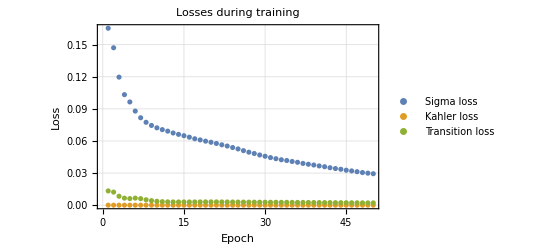

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

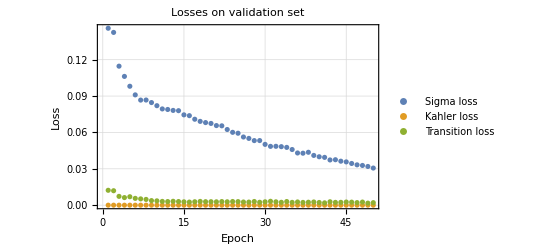

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

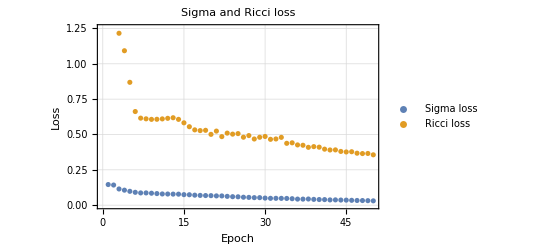

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

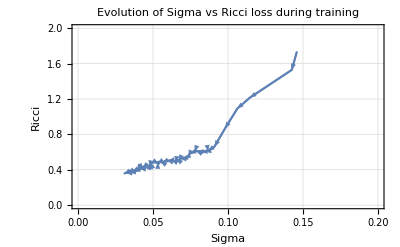

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",FrameLabel->{"Sigma","Ricci"},PlotRange->{{0,0.2},{0,2}},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

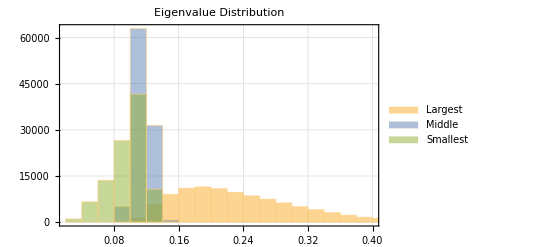

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```